```mathematica
(*Mathematica*)
```

```mathematica
Clear[ϕ,f,m,r,w,v,sc,g]
```

```mathematica
(*m016(32)*)
p[z_]=z^5-z^4-z^3+3*z^2-1
```

1-z+4 z^2-2 z^3-2 z^4+z^5

```mathematica
ϕ=N[GoldenRatio]
```

1.61803

```mathematica
Exp[2*π*I*ϕ]
```

-0.737369-0.67549 ⅈ

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[p[x],x]]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{-1,1,-4,2,2}}

```mathematica
N[Eigenvalues[m]]
```

{2.10296,-1.51984,1.3164,0.0502438+0.484923 ⅈ,0.0502438-0.484923 ⅈ}

```mathematica
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
```

```mathematica
v=Table[r[i],{i,5}]
```

{-1.51984,0.0502438-0.484923 ⅈ,0.0502438+0.484923 ⅈ,1.3164,2.10296}

```mathematica
Abs[%]
```

{1.51984,0.487519,0.487519,1.3164,2.10296}

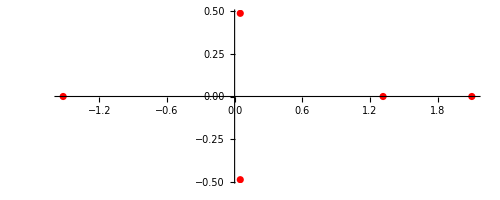

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
sc=2.0;
```

```mathematica
w={{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[1]],Im[r[1]]},{Re[r[3]],Im[r[3]]}},{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[2]],Im[r[2]]},{Re[r[3]],Im[r[3]]}},{{Re[r[2]],Im[r[2]]},{Re[r[4]],Im[r[4]]}},{{Re[r[3]],Im[r[3]]},{Re[r[4]],Im[r[4]]}}}
```

{{{-1.51984,0},{0.0502438,-0.484923}},{{-1.51984,0},{0.0502438,0.484923}},{{-1.51984,0},{0.0502438,-0.484923}},{{0.0502438,-0.484923},{0.0502438,0.484923}},{{0.0502438,-0.484923},{1.3164,0}},{{0.0502438,0.484923},{1.3164,0}}}

```mathematica
Table[Eigenvalues[w[[i]]]//Chop,{i,6}]
```

{{-1.51984,-0.484923},{-1.51984,0.484923},{-1.51984,-0.484923},{0.418819,0.116348},{0.0251219+0.798575 ⅈ,0.0251219-0.798575 ⅈ},{0.824487,-0.774243}}

```mathematica
(* Projecting the  3rd Minimal Pisot Polynomial onto a qz^(2*n) Hermann rings Julia*)
```

```mathematica
f[z_,1]=Exp[2*π*I*ϕ]*z^6*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,2]=Exp[2*π*I*ϕ]*z^8*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,3]=Exp[2*π*I*ϕ]*z^10*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,4]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,5]=Exp[2*π*I*ϕ]*z^14*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,6]=Exp[2*π*I*ϕ]*z^16*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
```

```mathematica
g=JuliaSetPlot[f[z,3],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All];
```

```mathematica
Export["Julia_5root_m016_3_2_z10_Herman_rings_Hue_scale2.jpg",g]
```

Julia_5root_m007neg5_1_z10_Herman_rings_Hue_scale2.jpg

```mathematica
(*end*)
```